# Métodos numéricos: Hoja 1

## Ejercicio 1:

Tenemos que encontrar las raíces aproximadas de la función f(x) que aparece en la hoja. Para ello, vamos a utilizar el método de la bisección en Fortran.

En Mathematica, la función f(x) tiene la siguiente forma y las siguientes soluciones para el intervalo [2,5]:

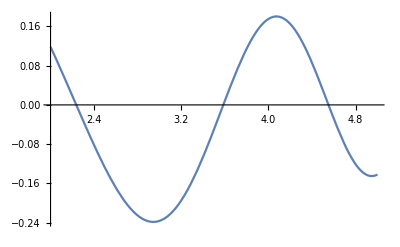

{x→2.2360679775}

{x→3.58524498939}

{x→4.55060031951}

```mathematica
f[x_]:=(1/2)*Exp[-x/4]*Sin[2-(2*x^2/5)]
Plot[f[x],{x,2,5}]
FindRoot[f[x]==0,{x,2,3},AccuracyGoal->20,WorkingPrecision->12,MaxIterations->100]
FindRoot[f[x]==0,{x,3,4},AccuracyGoal->20,WorkingPrecision->12,MaxIterations->100]
FindRoot[f[x]==0,{x,4,5},AccuracyGoal->20,WorkingPrecision->12,MaxIterations->100]
```

Vamos a utilizar una precisión de β = 10^-5.
Para el intervalo [2,3] el resultado obtenido es 2.23606109619.
Para el intervalo [3,4] el resultado es 3.58524322510.
Para el intervalo [4,5] tenemos 4.55060577393.
En todos los casos el bucle se ejecuta 16 veces y los resultados coinciden con la solución en Mathematica hasta la quinta cifra decimal.

## Ejercicio 2:

Ahora, debemos calcular las mismas raíces para la función del ejercicio anterior, pero utilizando el método de la secante.

Vamos a utilizar la precisión del apartado anterior.
Para el intervalo [2,3] el resultado es 2,23606797750 con 4 iteraciones coincidiendo todas las cifras decimales con la solución en Mathematica.
Para el intervalo [3,4] es 3.58524498720 con 3 iteraciones coincidiendo con la solución de Mathematica hasta la octava cifra decimal.
Para el intervalo [4,5] obtenemos 4.55060031962 con 3 iteraciones siendo igual con la solución del programa hasta la novena cifra decimal.

Se ve que este método es mucho más rápido y preciso que el de la bisección.

## Ejercicio 3:

Por último, vamos a utilizar el método de Newton-Raphson para calcular los máximos y mínimos en el intervalo [2,5]. Para ello hay que calcular la primera y segunda derivada de f[x], ya que los puntos que se hacen cero en la primera derivada son los máximos y mínimos de f[x].

En Mathematica calculamos las derivadas y sacamos los puntos de corte de f’[x]:

-1/40 ⅇ^(-x/4) (16 x Cos[2-(2 x^2)/5]+5 Sin[2-(2 x^2)/5])

1/800 ⅇ^(-x/4) (160 (-2+x) Cos[2-(2 x^2)/5]+(25-256 x^2) Sin[2-(2 x^2)/5])

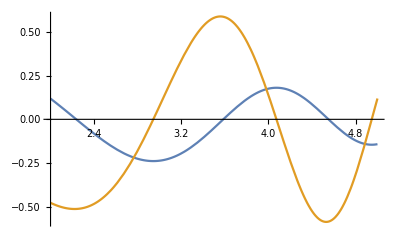

{x→2.94321949208}

{x→4.07302550547}

{x→4.94744923488}

```mathematica
Simplify[f'[x]]
Simplify[f''[x]]
Plot[{f[x],f'[x]},{x,2,5}]
FindRoot[f'[x]==0,{x,2.5,3.5},AccuracyGoal->20,WorkingPrecision->12,MaxIterations->100]
FindRoot[f'[x]==0,{x,3.5,4.5},AccuracyGoal->20,WorkingPrecision->12,MaxIterations->100]
FindRoot[f'[x]==0,{x,4.5,5},AccuracyGoal->20,WorkingPrecision->12,MaxIterations->100]
```

Los resultados obtenidos en Fortran con la precisión pedida son:
- 2.94321949208 hemos usado de punto de partida x=3.
- 4.07302550547 hemos usado de punto de partida x=4.
- 4.94744923488 donde hemos partido del punto x=5.
Siendo el número de iteraciones 2 y coinciden en todas las cifras.